# ZeckendorfRepresentation

ZeckendorfRepresentation[n]
gives the 0-1 list that indicates the unique nonconsecutive Fibonacci numbers that sum to the non-negative integer n.

The Fibonacci numbers here are considered to be 1, 2, 3, 5, …, not 1, 1, 2, 3, 5, …; otherwise, the representation would not be unique.

## See AlsoSeeAlsoInsert links to any related reference (function) pages.

Fibonacci ▪ IntegerDigits ▪ BaseForm ▪

## Tech NotesTechNotesInsert links to related tech notes.

## Related Guides

## Related LinksRelatedLinksInsert links to any related page, including web pages.

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`CombinatoricsPaclet`"]
```

## Basic Examples | More Examples ⊳

The first number whose representation takes three summands is 12:

```mathematica
ZeckendorfRepresentation[12]
```

{1,0,1,0,1}

This corresponds to 8 + 3 + 1:

```mathematica
Reverse@Fibonacci[{2,4,6}]
```

{8,3,1}

The first number whose representation takes four summands is 33:

```mathematica
ZeckendorfRepresentation[33]
```

{1,0,1,0,1,0,1}

```mathematica
With[{z=ZeckendorfRepresentation[33]},Prepend[Reverse@z,0].Fibonacci@Range[1+Length@z]]
```

33

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

### Generalizations & Extensions

### Options

### Applications

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

```mathematica
Fibonacci@6
```

8

There are F_k Zeckendorf representations of length k; for example, here are the 13 representations of length 7:

```mathematica
ZeckendorfRepresentation/@Range[21,33]//Grid
```

1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1

This visualizes the same pattern:

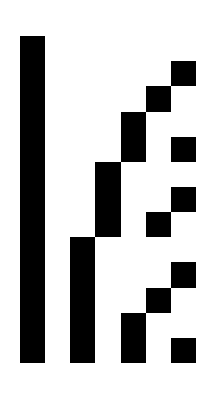

```mathematica
Framed@Graphics@Raster@Reverse[1-ZeckendorfRepresentation/@Range[21,33]]
```

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/CombinatoricsPaclet

PeterBurbery`CombinatoricsPaclet`

PeterBurbery/CombinatoricsPaclet/ref/ZeckendorfRepresentation

### Keywords

### Syntax Templates